```mathematica
k = {{0, -1}, {-1, 0}};
kt = MatrixExp[-0.1 * k]
```

{{1.005,0.100167},{0.100167,1.005}}

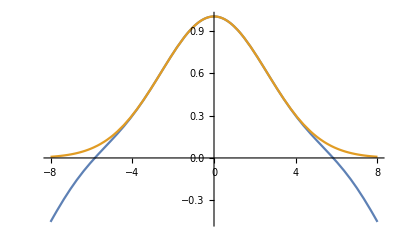

```mathematica
dt = 0.1;
U = 1.5 ;
eta = {0.8709650529539331,0.2767666333740771};
gamma = {0.2151952865677692,1.784804713432231};
f[n_]:= 1/2* (gamma[[1]] * Cos[eta[[1]] * n] + gamma[[2]] * Cos[eta[[2]] * n] );
Plot[{f[x], Exp[-dt*U/2*x^2]}, {x, -8, 8}]
```